```mathematica
ClearAll["Global`*"]
```

```mathematica
<<CustomTicks.m;
dataUS=Import["C:\\Users\\maeinss\\OneDrive\\ML\\Final_Project\\Covid\\dataUS.csv"]/.s_String :>ToExpression[s];
dataUK=Import["C:\\Users\\maeinss\\OneDrive\\ML\\Final_Project\\Covid\\dataUK.csv"]/.s_String :>ToExpression[s];
dataFr=Import["C:\\Users\\maeinss\\OneDrive\\ML\\Final_Project\\Covid\\dataFr.csv"]/.s_String :>ToExpression[s];
dataSp=Import["C:\\Users\\maeinss\\OneDrive\\ML\\Final_Project\\Covid\\dataSp.csv"]/.s_String :>ToExpression[s];
dataGer=Import["C:\\Users\\maeinss\\OneDrive\\ML\\Final_Project\\Covid\\dataGer.csv"]/.s_String :>ToExpression[s];
Import::fmterr: "Cannot import data as \!\(\*RowBox[{\"\\\"CSV\\\"\"}]\) format."
```

Cannot import data as `1` format.

```mathematica
data1={dataUS,dataUK,dataFr,dataSp,dataGer};
```

```mathematica
data=Table[Map[{#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],#[[8]],#[[9]]}&,data1[[i]][[2;;All]]],{i,Length[data1]}];
```

```mathematica
data[[1,1]]
```

{1,0,0,1,8,-5,0}

```mathematica
coun=1
```

1

```mathematica
data[[4,All,1]]//Length
```

93

```mathematica
fig1=ListLinePlot[{data[[coun,All,1]],data[[coun,All,5]]},PlotRange->{{20,Length[data[[coun,All,3]]]},All},AspectRatio->0.85,
PlotLegends->{Placed[LineLegend[{"Confirmed","Predicted"},LabelStyle->{FontFamily->"Times New Roman",FontSize->24,FontColor->Purple,FontSlant->Italic,FontWeight->"Heavy"},LegendMarkers->Graphics[{Thickness[0.2],Line[{{1,0},{9,0}}]}]],(*{Right,Bottom}*){0.45,.82}]},
PlotStyle->{{Blue,Thickness->0.005},{Red,Thickness->0.005}},
Frame->{True,True,False,False},
PlotLabel->Style["Cases",Black],
FrameLabel->{Row[{Style["Days",Italic],""}],Row[{Style["Number",Italic],""}]},
(*FrameTicks->{{LinTicks[0,9,2,2(*,ShowTickLabels->False*),MajorTickLength->0.02,MinorTickLength->0.008],None},{LinTicks[5,30,5,2,MajorTickLength->0.02,MinorTickLength->0.008],None}},*)
PlotRangePadding->0,
FrameStyle->{{Directive[Black],Thickness->0.004},{Directive[Black],Thickness->0.003},{Directive[Black],Thickness->0.003},{Directive[Black],Thickness->0.003}},
FrameTicksStyle->Directive[Black],BaseStyle->{FontSize->26}];
```

```mathematica
fig2=ListLinePlot[{data[[coun,All,2]],data[[coun,All,6]]},PlotRange->{{20,Length[data[[coun,All,3]]]},All},AspectRatio->0.85,
PlotLegends->{Placed[LineLegend[{"Confirmed","Predicted"},LabelStyle->{FontFamily->"Times New Roman",FontSize->24,FontColor->Purple,FontSlant->Italic,FontWeight->"Heavy"},LegendMarkers->Graphics[{Thickness[0.2],Line[{{1,0},{9,0}}]}]],(*{Right,Bottom}*){0.45,.82}]},
PlotStyle->{{Blue,Thickness->0.005},{Red,Thickness->0.005}},
Frame->{True,True,False,False},
PlotLabel->Style["Recovered",Black],
FrameLabel->{Row[{Style["Days",Italic],""}],Row[{Style["Number",Italic],""}]},
(*FrameTicks->{{LinTicks[0,9,2,2(*,ShowTickLabels->False*),MajorTickLength->0.02,MinorTickLength->0.008],None},{LinTicks[5,30,5,2,MajorTickLength->0.02,MinorTickLength->0.008],None}},*)
PlotRangePadding->0,
FrameStyle->{{Directive[Black],Thickness->0.004},{Directive[Black],Thickness->0.003},{Directive[Black],Thickness->0.003},{Directive[Black],Thickness->0.003}},
FrameTicksStyle->Directive[Black],BaseStyle->{FontSize->26}];
fig3=ListLinePlot[{data[[coun,All,3]],data[[coun,All,7]]},PlotRange->{{20,Length[data[[coun,All,3]]]},All},AspectRatio->0.85,
PlotLegends->{Placed[LineLegend[{"Confirmed","Predicted"},LabelStyle->{FontFamily->"Times New Roman",FontSize->24,FontColor->Purple,FontSlant->Italic,FontWeight->"Heavy"},LegendMarkers->Graphics[{Thickness[0.2],Line[{{1,0},{9,0}}]}]],(*{Right,Bottom}*){0.45,.82}]},
PlotStyle->{{Blue,Thickness->0.005},{Red,Thickness->0.005}},
Frame->{True,True,False,False},
PlotLabel->Style["Deaths",Black],
FrameLabel->{Row[{Style["Days",Italic],""}],Row[{Style["Number",Italic],""}]},
(*FrameTicks->{{LinTicks[0,9,2,2(*,ShowTickLabels->False*),MajorTickLength->0.02,MinorTickLength->0.008],None},{LinTicks[5,30,5,2,MajorTickLength->0.02,MinorTickLength->0.008],None}},*)
PlotRangePadding->0,
FrameStyle->{{Directive[Black],Thickness->0.004},{Directive[Black],Thickness->0.003},{Directive[Black],Thickness->0.003},{Directive[Black],Thickness->0.003}},
FrameTicksStyle->Directive[Black],BaseStyle->{FontSize->26}];
```

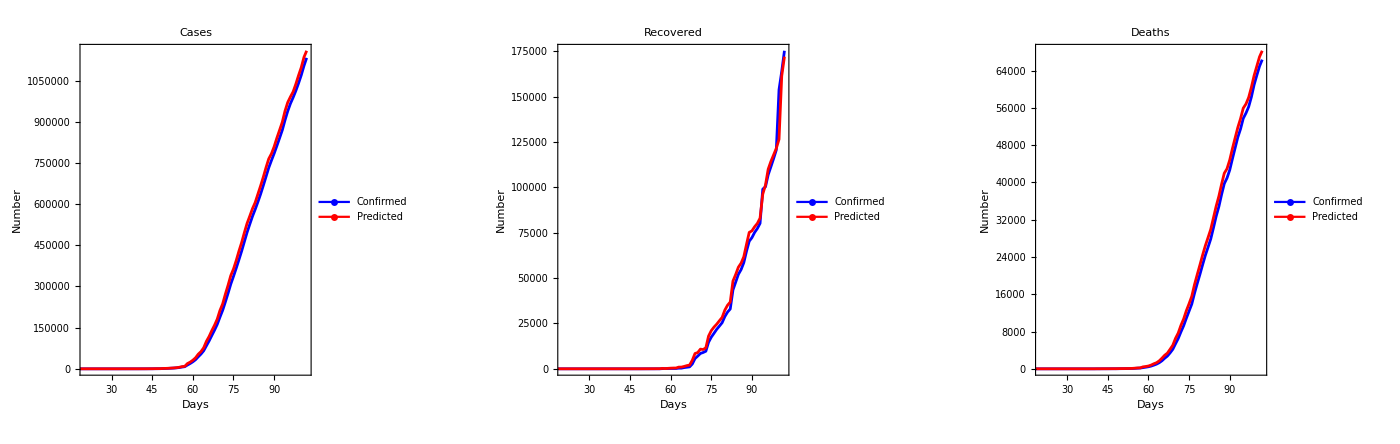

```mathematica
GraphicsRow[{fig1,fig2,fig3},ImageSize->1400]
```